```mathematica
(* input rho1, th1, rho2 , rho1p *)
eps=1/4;
rho1=1+95/100eps;
th1=.;
rho2=1+eps;
rho1p=1+eps/2;
(* normal component of velovity ofr altra-relativistic fluid *)
vinn=N[√((3 rho1 + 1)/(3(3 + rho1)))]
v1n1=N[√((3+rho1)/(3(3 rho1+ 1)))]
v1n2=N[√((3 rho2/rho1 + 1)/(3(3 + rho2/rho1)))]
v2n=N[√((3  + rho2/rho1)/(3(3 rho2/rho1 +1)))]
vinnp=N[√((3 rho1p + 1)/(3(3 + rho1p)))]
v1pn1=N[√((3+rho1p)/(3(3 rho1p+ 1)))]
v1pn2=N[√((3 rho2/rho1p + 1)/(3(3 + rho2/rho1p)))]
v2np=N[√((3  + rho2/rho1p)/(3(3 rho2/rho1p +1)))]
```

0.60885

0.54748

0.578803

0.575901

0.594588

0.560612

0.592749

0.562352

```mathematica
(* compute the velocities and angles *)
vin=N[{vinn,0}/Cos[th1]];
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=v1n1 n1 +vin.t1 t1;
a2=v1.v1;
a1=-2  v1n2 v1[[1]];
a0=v1n2^2 -v1[[2]]^2;
th2=N[ArcCos[(-a1+√(a1^2-4 a0 a2))/(2 a2)]];(* checked another root, no zero point in parallel checking *)
n2={Cos[th2],-Sin[th2]};
t2={Sin[th2],Cos[th2]};
v2=v2n n2 +v1.t2 t2;

th1p=N[ArcCos[vinnp/vinn Cos[th1]]];
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=v1pn1 n1p +vin.t1p t1p;
a2p=v1p.v1p;
a1p=-2 v1pn2 v1p[[1]];
a0p=v1pn2^2-v1p[[2]]^2;
th2p=N[ArcCos[(-a1p+√(a1p^2-4 a0p a2p))/(2 a2p)]];(* checked another root, another zero point, but wrong direction *)
n2p={Cos[th2p],Sin[th2p]};
t2p={Sin[th2p],- Cos[th2p]};
v2p=v2np n2p +v1p.t2p t2p;
```

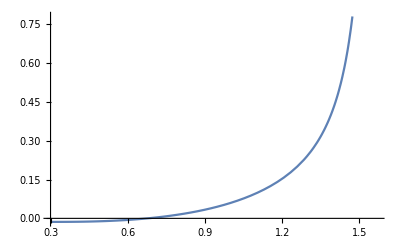

```mathematica
(* v2 and v2p are parallel *)
Plot[v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]],{th1,.3,1.57}]
```

```mathematica
th1r=FindRoot[v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]],{th1,0.79}]
```

{th1→0.676586}

```mathematica
(* output the results *)
```

```mathematica
th1=th1/.th1r;
vin=N[{vinn,0}/Cos[th1]]
n1={Cos[th1],Sin[th1]};
t1={-Sin[th1],Cos[th1]};
v1=v1n1 n1 +vin.t1 t1
a2=v1.v1;
a1=-2  v1n2 v1[[1]];
a0=v1n2^2 -v1[[2]]^2;
th2=N[ArcCos[(-a1+√(a1^2-4 a0 a2))/(2 a2)]]
n2={Cos[th2],-Sin[th2]};
t2={Sin[th2],Cos[th2]};
v2=v2n n2 +v1.t2 t2
th1p=N[ArcCos[vinnp/vinn Cos[th1]]];
n1p={Cos[th1p],-Sin[th1p]};
t1p={-Sin[th1p],-Cos[th1p]};
v1p=v1pn1 n1p +vin.t1p t1p
a2p=v1p.v1p;
a1p=-2 v1pn2 v1p[[1]];
a0p=v1pn2^2-v1p[[2]]^2;
th2p=N[ArcCos[(-a1p+√(a1p^2-4 a0p a2p))/(2 a2p)]]
n2p={Cos[th2p],Sin[th2p]};
t2p={Sin[th2p],- Cos[th2p]};
v2p=v2np n2p +v1p.t2p t2p
```

{0.780862,0.}

{0.733012,-0.0384256}

0.609991

{0.694548,-0.0115434}

{0.754991,0.0220243}

0.639302

{0.709506,-0.011792}

```mathematica
(* check parallelism *)
v2[[1]] v2p[[2]]-v2[[2]]v2p[[1]]
```

-3.55618×10^-16

```mathematica
(*****************************************************)
(* HERE ARE ALL THE NUMERICAL VALUES FOR THE DENSITIES, ANGLES (IN RADIANS) AND VELOCITIES*)
(* Density in units of incoming unperturbed density, in regions 1, 2 and 1prime as labelled in diagram *)
N[rho1]
```

1.2375

```mathematica
N[rho1p]
```

1.125

```mathematica
N[rho2]
```

1.25

```mathematica
th1
```

0.676586

```mathematica
th2
```

0.609991

```mathematica
th1p
```

0.705248

```mathematica
th2p
```

0.639302

```mathematica
vin
```

{0.780862,0.}

```mathematica
v1
```

{0.733012,-0.0384256}

```mathematica
v2
```

{0.694548,-0.0115434}

```mathematica
v1p
```

{0.754991,0.0220243}

```mathematica
v2p
```

{0.709506,-0.011792}

```mathematica
(* this is the velocity jump *)
```

```mathematica
v2-v2p
```

{-0.0149574,0.000248592}

```mathematica
(* check that the two velocities on either side of the slip line are parallel *)
v2p[[1]]v2[[2]]-v2p[[2]]v2[[1]]
```

3.55618×10^-16